```mathematica
Get["C:\\Users\\Hp\\Desktop\\PREDMETI\\3._letnik\\1._semester\\NROR\\DN\\DN2\\generiranje_točk.m"]
gen[100000]
```

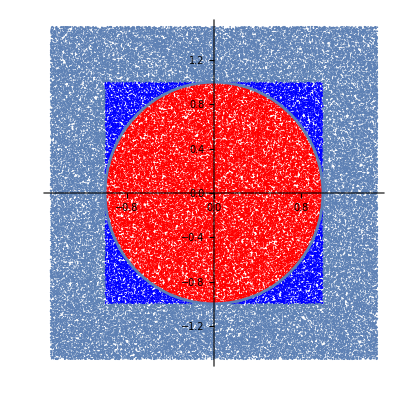

```mathematica
krog1=ListPlot[krog,PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1,PlotStyle->Red];
kvadrat1=ListPlot[kvadrat,PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1,PlotStyle->Blue];
izven1=ListPlot[izven,PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1PlotStyle->Black];
krožnica=ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5}];
Show[krog1,kvadrat1,izven1,krožnica]
```

```mathematica
aproksimacija=4.*Length[krog]/(Length[krog]+Length[kvadrat]);
napaka=aproksimacija-π;
Print["aproksimacija: ",aproksimacija,"\nnapaka: ",napaka]
```

aproksimacija: 3.14023
napaka: -0.00136545